```mathematica
h=8;
V=15;
```

```mathematica
x0=8;
y0=0;
```

```mathematica
bsbe =FindRoot[{-(h/2)*(Log[(Cos[be/2]+Sin[be/2])/(Cos[be/2]-Sin[be/2])]-Log[(Cos[bs/2]+Sin[bs/2])/(Cos[bs/2]-Sin[bs/2])]+(1/Cos[bs]-2/Cos[be])*Tan[bs]+Tan[be]/Cos[be])==x0,h*((1/(Cos[bs]) - 1/Cos[be]))==y0},{{bs,2.5},{be,4}}]
```

{bs→2.69249+0. ⅈ,be→3.59069+0. ⅈ}

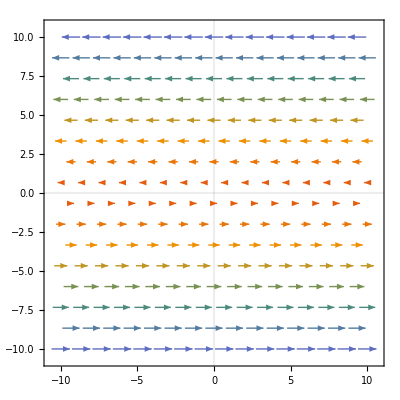

```mathematica
field=VectorPlot[{-(V/h)*y,0},{x,-10,10},{y,-10,10},VectorScaling->Automatic,VectorSizes->Automatic,PlotTheme->"Scientific"]
```

```mathematica
ts=0;
tend=Solve[{Tan[bs]-Tan[be]==(V/h)*(ts-te)}/.bsbe,te]
time={t,ts,Re[te/.tend]};
eqs={x'[t]==V*Cos[b[t]]-(V/h)*y[t],
y'[t]==V*Sin[b[t]],
b'[t]==(V/h)*(Cos[b[t]])^2};
```

{{te→0.514074+0. ⅈ}}

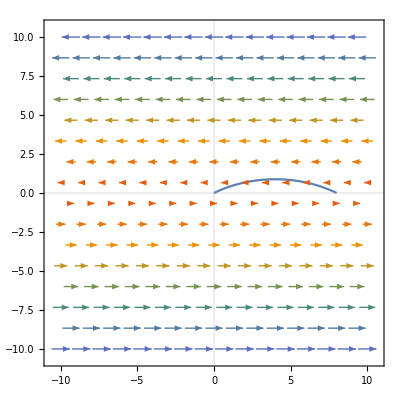

```mathematica
sol=NDSolve[Join[eqs,{x[0]==x0,y[0]==y0,b[0]==Re[bs/.bsbe]}],{x[t],y[t],b[t]},time];
trajektorie=ParametricPlot[{x[t],y[t]}/.sol,{t,ts,0.5140741935534169},Frame->True,GridLines->Automatic,PlotRange->{{-10,10},{-10,10}}];
Show[field,trajektorie]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
&Silnější pole 

h=2;
V=15;
```

```mathematica
x0=-2;
y0=5;
```

```mathematica
bsbe =FindRoot[{-(h/2)*(Log[(Cos[be/2]+Sin[be/2])/(Cos[be/2]-Sin[be/2])]-Log[(Cos[bs/2]+Sin[bs/2])/(Cos[bs/2]-Sin[bs/2])]+(1/Cos[bs]-2/Cos[be])*Tan[bs]+Tan[be]/Cos[be])==x0,h*((1/(Cos[bs]) - 1/Cos[be]))==y0},{{bs,5.5},{be,1}}]
```

{bs→4.95519,be→0.923977}

```mathematica
field=VectorPlot[{-(V/h)*y,0},{x,-10,10},{y,-10,10},VectorScaling->Automatic,VectorSizes->Automatic,PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
ts=0;
tend=Solve[{Tan[bs]-Tan[be]==(V/h)*(ts-te)}/.bsbe,te]
time={t,ts,Re[te/.tend]};
eqs={x'[t]==V*Cos[b[t]]-(V/h)*y[t],
y'[t]==V*Sin[b[t]],
b'[t]==(V/h)*(Cos[b[t]])^2};
```

{{te→0.714866}}

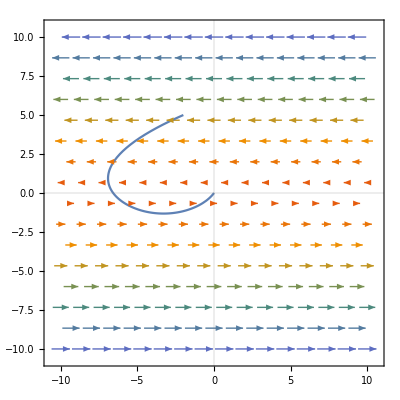

```mathematica
sol=NDSolve[Join[eqs,{x[0]==x0,y[0]==y0,b[0]==Re[bs/.bsbe]}],{x[t],y[t],b[t]},time];
trajektorie=ParametricPlot[{x[t],y[t]}/.sol,{t,ts,0.7148656434783358},Frame->True,GridLines->Automatic,PlotRange->{{-10,10},{-10,10}}];
Show[field,trajektorie]
```